```mathematica
zero=Select[Table[With[{g=CompleteGraph[8],h=Graph[edges]},
With[{res=EdgeDelete[g,EdgeList[h]]},
If[ChromaticPolynomial[res,4]==0,
edges]
]
],
{edges,{{4<->5,3<->6,2<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->7,1<->8},{4<->5,3<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->7,1<->5,1<->4},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->2},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->6,1<->3},{4<->5,3<->6,2<->5,2<->6,2<->7,1<->5,1<->4},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->7},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->5,1<->4,1<->7},{4<->5,3<->5,3<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->4,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->3},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->2},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->6},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->3,1<->5,1<->6}}}
],#=!=Null&]
```

{{4<->5,3<->6,2<->5,2<->6,2<->7,1<->7,1<->3},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->7},{4<->5,3<->5,3<->6,2<->6,2<->4,1<->5,1<->4,1<->7},{4<->5,3<->5,3<->4,2<->5,2<->4,2<->6,1<->6,1<->3}}

```mathematica
RemoveEdges[edges_]:=Block[{g=EdgeDelete[CompleteGraph[8],edges],nonedges},
nonedges=EdgeList[g];
Table[
With[{h=Graph[EdgeDelete[g,e],VertexLabels->"Name"]},
{Labeled[h,EdgeCount[h]],ChromaticPolynomial[h,4],PlanarGraphQ[h]}
]
,{e,Subsets[nonedges,{10-Length[edges]}]}
]
]
```

```mathematica
3*8-6
```

18

```mathematica
Binomial[8,2]
```

28

```mathematica
all=Flatten[Table[RemoveEdges[e],{e,zero}],1];
```

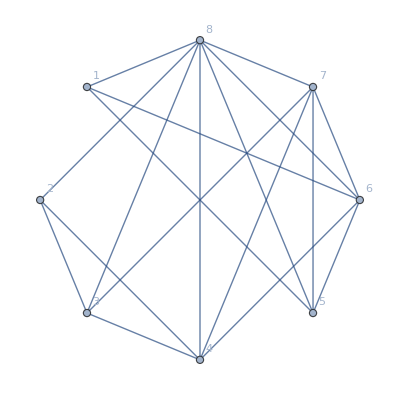
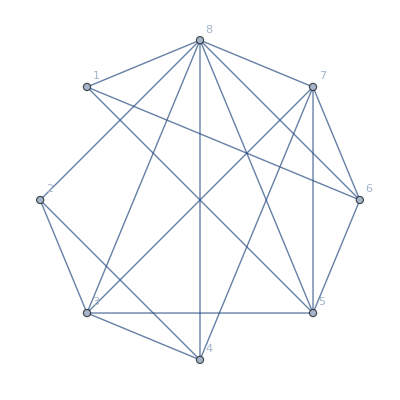
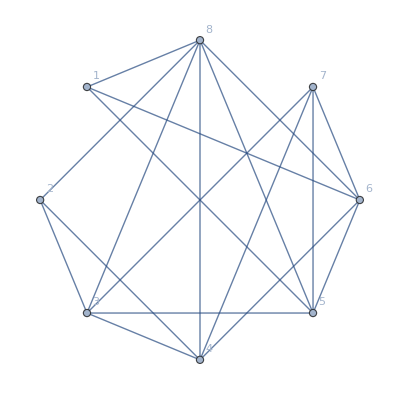
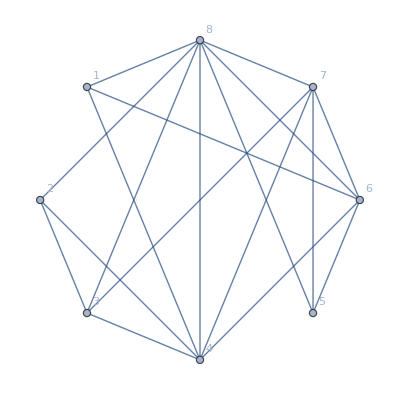
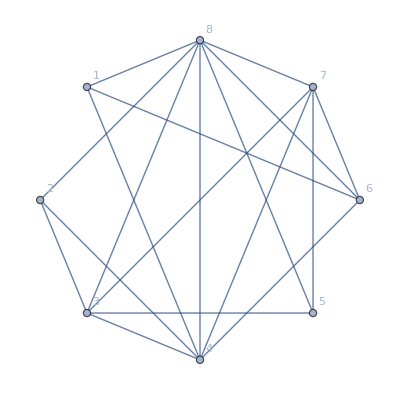
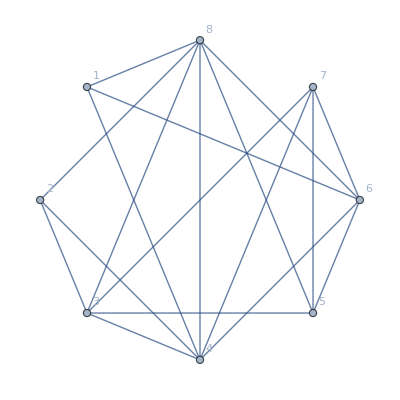
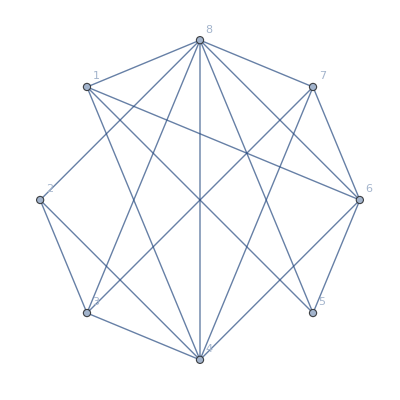
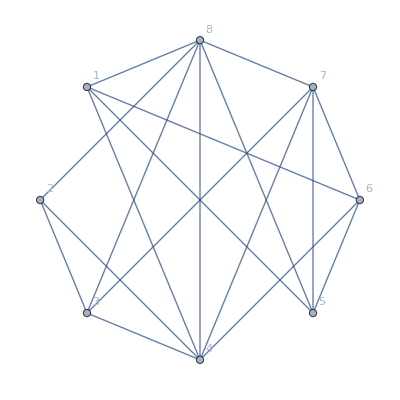
{{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,96,True},{-Graphics-18,72,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,72,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,72,True},{-Graphics-18,72,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,72,True},{-Graphics-18,72,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,72,True},{-Graphics-18,120,True},{-Graphics-18,72,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,288,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,288,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,96,True},{-Graphics-18,288,True},{-Graphics-18,288,True},{-Graphics-18,120,True},{-Graphics-18,288,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,96,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,96,True},{-Graphics-18,120,True},{-Graphics-18,120,True},{-Graphics-18,96,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,120,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True},{-Graphics-18,24,True}}

```mathematica
Select[all,#[[3]]&]
```

```mathematica
Tally[Sort[Flatten[Table[RemoveEdges[e],{e,zero}],1],#1[[2]]<#2[[2]]&],IsomorphicGraphQ[#1[[1]],#2[[1]]]&]
```

{{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},{{-Graphics-18,0,False},1},8991,{{-Graphics-18,312,False},1},{{-Graphics-18,312,False},1},{{-Graphics-18,312,False},1},{{-Graphics-18,312,False},1},{{-Graphics-18,312,False},1},{{-Graphics-18,312,False},1},{{-Graphics-18,312,False},1},{{-Graphics-18,432,False},1},{{-Graphics-18,432,False},1},{{-Graphics-18,432,False},1},{{-Graphics-18,432,False},1},{{-Graphics-18,432,False},1},{{-Graphics-18,432,False},1},{{-Graphics-18,432,False},1},{{-Graphics-18,432,False},1},{{-Graphics-18,432,False},1},{{-Graphics-18,432,False},1}}
 |  |  |  |